## Numerical for 3 Flavor Neutrino Oscillation in Matter

### Prep

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/Dropbox/Research/git/15summer/assets

Avogadro number

```mathematica
nAvo=6*10^(23)
```

600000000000000000000000

```mathematica
gF=1.17*10^(-5);
```

### Numerical

```mathematica
numDen[x_]=10^(-12-4.3 x)
```

10^(-12-4.3 x)

```mathematica
theta12=33.36/180*Pi;
theta13=8.66/180*Pi;
theta23=40/180*Pi;
deltacp=0;
(*deltacp=300/180*Pi;*)
m1sq=0.01*10^(-18);
m2sq=m1sq+0.000079*10^(-18);
m3sq=m2sq+0.0027*10^(-18);
rS = 10^(24);
omega=10^(-19);
rSomega=rS*omega;
```

```mathematica
pmns={{Cos[theta12]Cos[theta13],Sin[theta12]Cos[theta13],Sin[theta13]Exp[-I deltacp]},{-Sin[theta12]Cos[theta23]-Cos[theta12]Sin[theta23]Sin[theta13]Exp[I deltacp],Cos[theta12]Cos[theta23]-Sin[theta12]Sin[theta23]Sin[theta13]Exp[I deltacp],Sin[theta23]Cos[theta13]},{Sin[theta12]Sin[theta23]-Cos[theta12]Cos[theta23]Sin[theta13]Exp[I deltacp],-Cos[theta12]Sin[theta23]-Sin[theta12]Cos[theta23]Sin[theta13]Exp[I deltacp],Cos[theta23]Cos[theta13]}}
%//MatrixForm
```

{{0.82571,0.543629,0.150571},{-0.502084,0.586603,0.635459},{0.257129,-0.600304,0.757311}}

(0.82571 | 0.543629 | 0.150571
-0.502084 | 0.586603 | 0.635459
0.257129 | -0.600304 | 0.757311)

```mathematica
hamilV=rSomega pmns.{{m1sq,0,0},{0,m2sq,0},{0,0,m3sq}}.Transpose[pmns];
```

```mathematica
hamilM[x_]=(hamilV+rSomega{{Sqrt[2]gF numDen[x],0,0},{0,0,0},{0,0,0}})*10^(16)//Simplify
```

{{10.0864+16546.3 ⅇ^(-9.90112 x),0.291092,0.291105},{0.291092,11.1494,1.30955},{0.291105,1.30955,11.6223}}

```mathematica
nuF3M[x_]={nuF3Me[x],nuF3Mm[x],nuF3Mt[x]}
```

{nuF3Me[x],nuF3Mm[x],nuF3Mt[x]}

```mathematica
matOsc3 = I nuF3M'[x]==hamilM[x].nuF3M[x]
```

{ⅈ nuF3Me'[x],ⅈ nuF3Mm'[x],ⅈ nuF3Mt'[x]}=={(10.0864+16546.3 ⅇ^(-9.90112 x)) nuF3Me[x]+0.291092 nuF3Mm[x]+0.291105 nuF3Mt[x],0.291092 nuF3Me[x]+11.1494 nuF3Mm[x]+1.30955 nuF3Mt[x],0.291105 nuF3Me[x]+1.30955 nuF3Mm[x]+11.6223 nuF3Mt[x]}

```mathematica
sol3M=NDSolve[matOsc3&&nuF3M[0]=={1,0,0},{nuF3Me,nuF3Mm,nuF3Mt},{x,0,2000}]
```

{{nuF3Me→InterpolatingFunction[{{0., 2000.}}, <>],nuF3Mm→InterpolatingFunction[{{0., 2000.}}, <>],nuF3Mt→InterpolatingFunction[{{0., 2000.}}, <>]}}

```mathematica
probesqrt=nuF3Me/.sol3M[[1]]
probmsqrt=nuF3Mm/.sol3M[[1]]
probtsqrt=nuF3Mt/.sol3M[[1]]
```

InterpolatingFunction[{{0., 2000.}}, <>]

InterpolatingFunction[{{0., 2000.}}, <>]

InterpolatingFunction[{{0., 2000.}}, <>]

```mathematica
norm[x_]=Abs[probesqrt[x]]^2+Abs[probmsqrt[x]]^2+Abs[probtsqrt[x]]^2
```

Abs[InterpolatingFunction[{{0., 2000.}}, <>][x]]^2+Abs[InterpolatingFunction[{{0., 2000.}}, <>][x]]^2+Abs[InterpolatingFunction[{{0., 2000.}}, <>][x]]^2

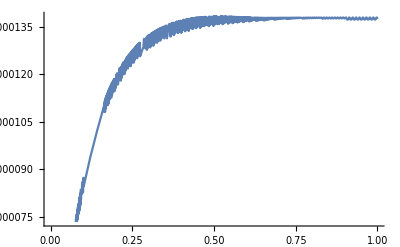

```mathematica
Plot[norm[x],{x,0,1}]
```

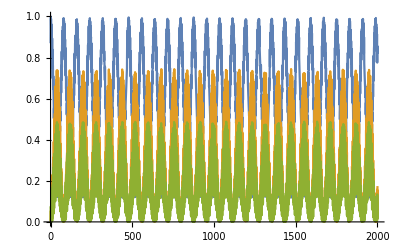

```mathematica
Plot[{Abs[probesqrt[x]]^2/norm[x],Abs[probmsqrt[x]]^2/norm[x],Abs[probtsqrt[x]]^2/norm[x]},{x,0,2000}]
```

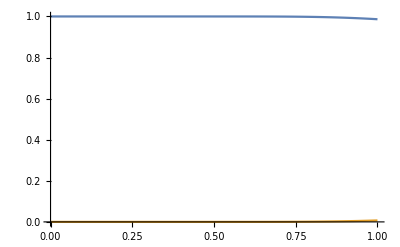

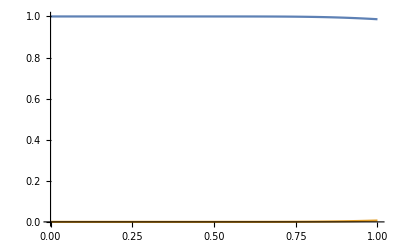

```mathematica
Plot[{Abs[probesqrt[x]]^2/norm[x],Abs[probtsqrt[x]]^2/norm[x]},{x,0,1}]
Plot[{Abs[probesqrt[x]]^2/norm[x],Abs[probmsqrt[x]]^2/norm[x]},{x,0,1}]
```

### In Vacuum Mass State Basis

```mathematica
numDen2[x_]=10^(-12-4.3 x)
```

10^(-12-4.3 x)

```mathematica
epSun= 10^(-24)
deltaH[x_]=√2 gF numDen2[x]/epSun
deltam12sq=7.6*10^(-5)*10^(-18)
deltam13sq=2.3*10^(-3)*10^(-18)
deltam23sq=deltam13sq-deltam12sq
ene=10^(-3)
```

1/1000000000000000000000000

0.0000165463 10^(12-4.3 x)

7.6×10^-23

2.3×10^-21

2.224×10^-21

1/1000

```mathematica
hamilMVM[x_]={{deltaH[x] pmns[[1,1]]^2-deltaH[x]/3+(deltam12sq+deltam13sq)/(6ene epSun),deltaH[x] pmns[[1,1]]pmns[[1,2]],deltaH[x] pmns[[1,1]] pmns[[1,3]]},{deltaH[x] pmns[[1,2]] pmns[[1,1]],deltaH[x] pmns[[1,2]]^2-deltaH[x]/3+(deltam12sq+deltam23sq)/(6ene epSun),deltaH[x]pmns[[1,2]]pmns[[1,3]]},{deltaH[x] pmns[[1,1]] pmns[[1,3]],deltaH[x] pmns[[1,2]] pmns[[1,3]],deltaH[x] pmns[[1,3]]^2-deltaH[x]/3+(deltam13sq+deltam23sq)/(6ene epSun)}}//FullSimplify
%//MatrixForm
```

{{396000.+5.76578×10^6 ⅇ^(-9.90112 x),7.42729×10^6 ⅇ^(-9.90112 x),2.05716×10^6 ⅇ^(-9.90112 x)},{7.42729×10^6 ⅇ^(-9.90112 x),383333.-625473. ⅇ^(-9.90112 x),1.35439×10^6 ⅇ^(-9.90112 x)},{2.05716×10^6 ⅇ^(-9.90112 x),1.35439×10^6 ⅇ^(-9.90112 x),754000.-5.1403×10^6 ⅇ^(-9.90112 x)}}

(396000.+5.76578×10^6 ⅇ^(-9.90112 x) | 7.42729×10^6 ⅇ^(-9.90112 x) | 2.05716×10^6 ⅇ^(-9.90112 x)
7.42729×10^6 ⅇ^(-9.90112 x) | 383333.-625473. ⅇ^(-9.90112 x) | 1.35439×10^6 ⅇ^(-9.90112 x)
2.05716×10^6 ⅇ^(-9.90112 x) | 1.35439×10^6 ⅇ^(-9.90112 x) | 754000.-5.1403×10^6 ⅇ^(-9.90112 x))

```mathematica
nuF3MVM[x_]={nuF3MVM1[x],nuF3MVM2[x],nuF3MVM3[x]}
```

{nuF3MVM1[x],nuF3MVM2[x],nuF3MVM3[x]}

```mathematica
matOsc3VM = I nuF3MVM'[x]==hamilMVM[x].nuF3MVM[x]
```

{ⅈ nuF3MVM1'[x],ⅈ nuF3MVM2'[x],ⅈ nuF3MVM3'[x]}=={(396000.+5.76578×10^6 ⅇ^(-9.90112 x)) nuF3MVM1[x]+7.42729×10^6 ⅇ^(-9.90112 x) nuF3MVM2[x]+2.05716×10^6 ⅇ^(-9.90112 x) nuF3MVM3[x],7.42729×10^6 ⅇ^(-9.90112 x) nuF3MVM1[x]+(383333.-625473. ⅇ^(-9.90112 x)) nuF3MVM2[x]+1.35439×10^6 ⅇ^(-9.90112 x) nuF3MVM3[x],2.05716×10^6 ⅇ^(-9.90112 x) nuF3MVM1[x]+1.35439×10^6 ⅇ^(-9.90112 x) nuF3MVM2[x]+(754000.-5.1403×10^6 ⅇ^(-9.90112 x)) nuF3MVM3[x]}

Initial conditions

```mathematica
initCon=Transpose[pmns].{1,0,0}
```

{0.82571,0.543629,0.150571}

```mathematica
sol3MVM=NDSolve[matOsc3VM&&nuF3MVM[0]==initCon,{nuF3MVM1,nuF3MVM2,nuF3MVM3},{x,0,1}]
```

{{nuF3MVM1→InterpolatingFunction[{{0., 1.}}, <>],nuF3MVM2→InterpolatingFunction[{{0., 1.}}, <>],nuF3MVM3→InterpolatingFunction[{{0., 1.}}, <>]}}

In terms of flavor eigenstates

```mathematica
prob1sqrtVM=nuF3MVM1/.sol3MVM[[1]]
prob2sqrtVM=nuF3MVM2/.sol3MVM[[1]]
prob3sqrtVM=nuF3MVM3/.sol3MVM[[1]]
```

InterpolatingFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
probsqrtDataVM=Table[{prob1sqrtVM[i],prob2sqrtVM[i],prob3sqrtVM[i]},{i,0,1,0.001}]
```

{{0.82571+0. ⅈ,0.543629+0. ⅈ,0.150571+0. ⅈ},{-0.23333+0.792029 ⅈ,-0.153235+0.52073 ⅈ,-0.0446777+0.150769 ⅈ},997,{0.00190123+0.00284228 ⅈ,0.000296569+0.000179932 ⅈ,-0.617442+0.878843 ⅈ},{0.00277834+0.00159151 ⅈ,0.000287538+0.000105719 ⅈ,-0.809488+0.706016 ⅈ}}
 |  |  |  |

```mathematica
Export["probsqrtDataVM.dat",probsqrtDataVM]
```

probsqrtDataVM.dat

```mathematica
len=Length@probsqrtDataVM
```

1001

```mathematica
probsqrtVM=Table[pmns.probsqrtDataVM[[i]],{i,1,Length@probsqrtDataVM}]
```

{{1.+0. ⅈ,-8.32667×10^-17+0. ⅈ,4.16334×10^-17+0. ⅈ},{-0.282693+0.959771 ⅈ,-0.00112796+0.00360474 ⅈ,-0.00184293+0.00523619 ⅈ},997,{-0.0912376+0.134773 ⅈ,-0.39314+0.557148 ⅈ,-0.467285+0.66618 ⅈ},{-0.119435+0.107677 ⅈ,-0.515623+0.447907 ⅈ,-0.612492+0.535019 ⅈ}}
 |  |  |  |

```mathematica
probesqrtVM=Table[probsqrtVM[[i,1]],{i,1,Length@probsqrtDataVM}];
probmsqrtVM=Table[probsqrtVM[[i,2]],{i,1,Length@probsqrtDataVM}];
probtsqrtVM=Table[probsqrtVM[[i,3]],{i,1,Length@probsqrtDataVM}];
```

```mathematica
normVM=Table[Abs[probesqrtVM[x]]^2+Abs[probmsqrtVM[x]]^2+Abs[probtsqrtVM[x]]^2,{x,1,len}]
```

$Aborted[]

```mathematica
normVM[1]
```

Abs[(0.635459 InterpolatingFunction[{{0., 1.}}, <>]+0.586603 InterpolatingFunction[{{0., 1.}}, <>]-0.502084 InterpolatingFunction[{{0., 1.}}, <>])[0.5]]^2+Abs[(0.757311 InterpolatingFunction[{{0., 1.}}, <>]-0.600304 InterpolatingFunction[{{0., 1.}}, <>]+0.257129 InterpolatingFunction[{{0., 1.}}, <>])[0.5]]^2+Abs[(0.150571 InterpolatingFunction[{{0., 1.}}, <>]+0.543629 InterpolatingFunction[{{0., 1.}}, <>]+0.82571 InterpolatingFunction[{{0., 1.}}, <>])[0.5]]^2

```mathematica
Plot[normVM[x],{x,0,1},PlotLabel->"Normalization Factor",Frame->True,ImageSize->Large]
```

-Graphics-

```mathematica
Plot[{Abs[probesqrtVM[x]]^2/normVM[x],Abs[probmsqrtVM[x]]^2/normVM[x],Abs[probtsqrtVM[x]]^2/normVM[x]},{x,0,1},PlotLabel->"Probability for ",Frame->True,ImageSize->Large,PlotLegends->Placed[{"ν_1","ν_2","ν_3"},{Center,Above}]]
```

-Graphics-